# 0D-Voltage-Current-SoC Model Applied to The MV-TMATEMPO System

```mathematica
Needs["ZeroDimVoltageCurrentSocModel`",FileNameJoin[{NotebookDirectory[],"ZeroDimVoltageCurrentSocModel.wl"}]];
```

## Initialize Model and Perform Model Checks

```mathematica
initModel[];
checkModel[];
```

## Visualize Amount of Substance vs SoC

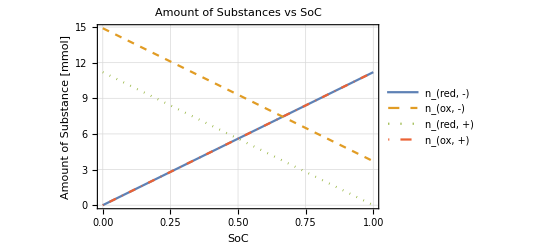

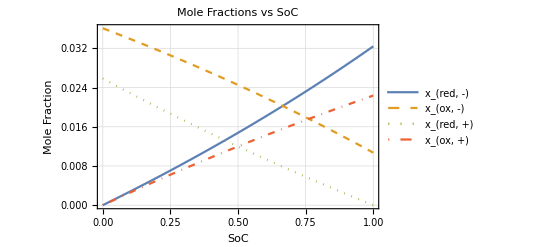

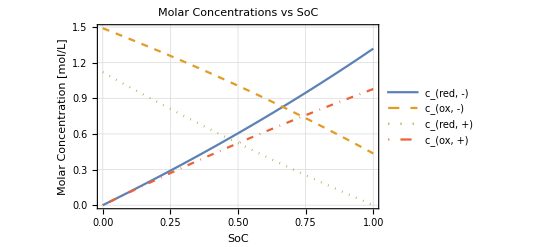

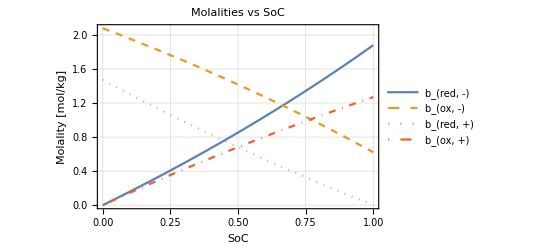

```mathematica
pElectroActiveSpeciesMoles=plotElectroActiveSpeciesMoles[]
pElectroActiveSpeciesMoleFractions=plotElectroActiveSpeciesMoleFractions[]
pElectroActiveSpeciesMolarities=plotElectroActiveSpeciesMolarities[]
pElectroActiveSpeciesMolalities=plotElectroActiveSpeciesMolalities[]
```

## Approximate Electrolyte Volume Changes

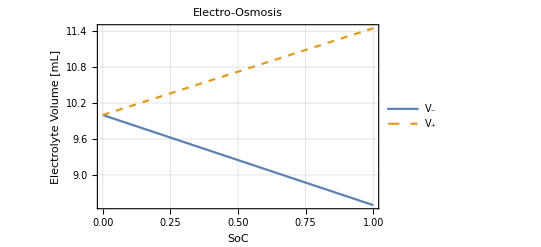

```mathematica
pElectrolyteVolume=plotElectrolyteVolume[]
```

## Cell Voltage & Power Density vs SoC

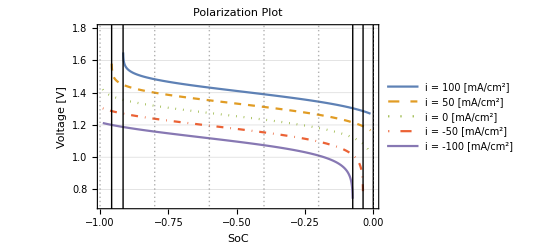

```mathematica
plotCellVoltageVsSoc[{lstElCurrentDensities->{100,50,0,-50,-100}}]
```

## Cell Voltage & Power Density vs El. Current Density

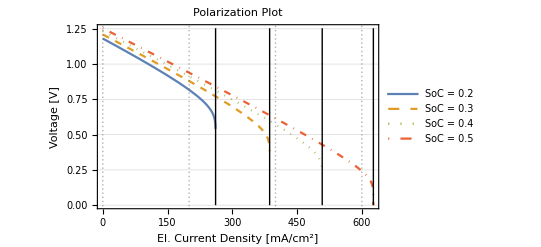

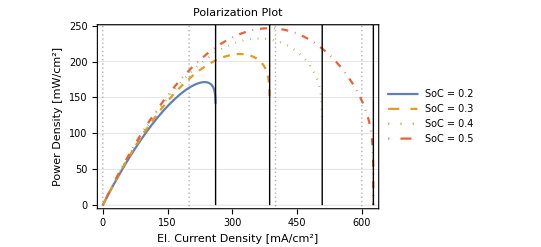

```mathematica
plotCellVoltageVsElCurrentDensity[{lstSoc-> {0.2,0.3,0.4,0.5}}]
plotCellPowerDensityVsElCurrentDensity[{lstSoc-> {0.2,0.3,0.4,0.5}}]
```

## Visualize Losses (Activation, Concentration, Ohmic)

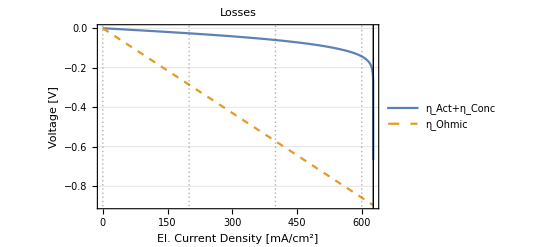

```mathematica
plotVoltageLossesVsElCurrentDensity[{soc-> 0.5}]
```

## Show Voltage & Power Density vs SoC and El. Current Density

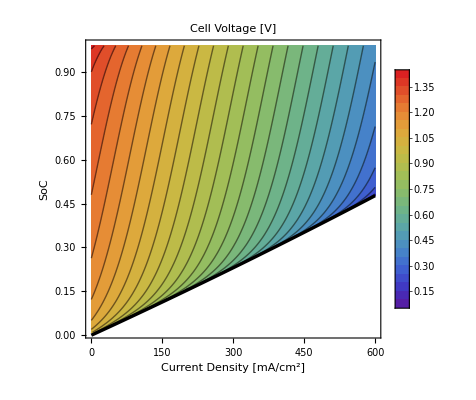

```mathematica
plotCellVoltageVsSocAndCurrentDensity[]
```

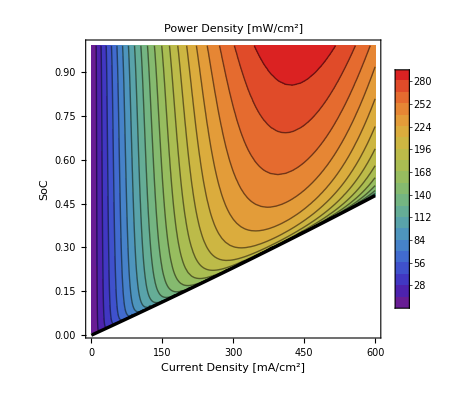

```mathematica
plotCellPowerDensityVsSocAndCurrentDensity[]
```

## Sensitivity Studies

### Flow Rate

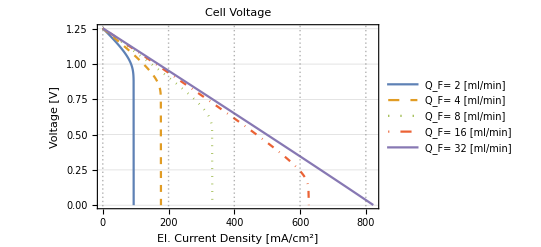

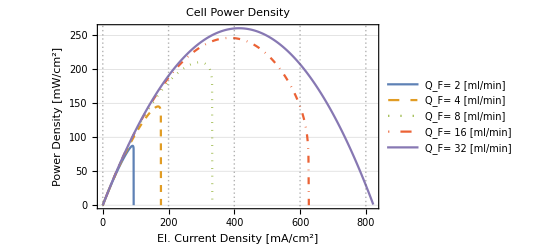

```mathematica
{cellVoltageVsElCurrentDensityPlot,powerDensityVsElCurrentDensityPlot}=plotCellPerformanceForDifferentFlowRates[{soc-> 0.5,lstFlowRates-> {2,4,8,16,32}*1/(60*10^6),ImageSize-> 400}];
Show[cellVoltageVsElCurrentDensityPlot]
Show[powerDensityVsElCurrentDensityPlot]
```

## Miscellaneous Plots

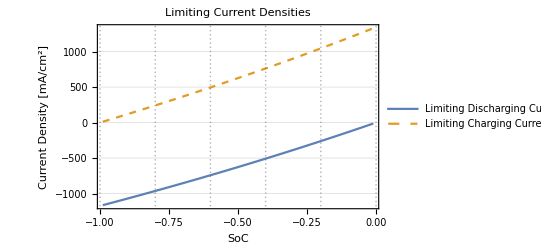

```mathematica
plotLimitingElCurrentDensity[]
```

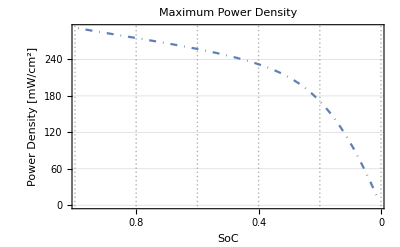

```mathematica
plotMaximumPowerDensity[]
```

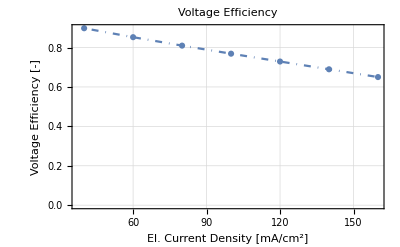

```mathematica
plotVoltageEfficiency[{elCurrentDensityStepSize->20,lowVoltageCutoff-> 0.9,highVoltageCutoff->1.5}]
```